```mathematica
SetDirectory["D:\\VELA\\GIT Projects\\Software\\Apps\\RF_Conditioner\\logs\\data"]
```

D:\VELA\GIT Projects\Software\Apps\RF_Conditioner\logs\data

```mathematica
typemap=<|"<class 'VELA_CLARA_enums.STATE'>"->"Byte","<class 'VELA_CLARA_RF_Modulator_Control.GUN_MOD_STATE'>"->"Byte","<class 'VELA_CLARA_RF_Protection_Control.RF_GUN_PROT_STATUS'>"->"Byte","<class 'VELA_CLARA_Vac_Valve_Control.VALVE_STATE'>"->"Byte","<type 'bool'>"->"Byte","<type 'float'>"->"Real32","<type 'int'>"->"Integer32","<type 'long'>"->"Integer32"|>;
```

```mathematica
Lookup[typemap,types]
```

{Real32,Real32,Real32,Integer32,Integer32,Real32,Real32,Real32,Byte,Real32,Real32,Real32,Real32,Byte,Byte,Real32,Byte,Real32,Integer32,Real32,Byte,Byte,Real32,Byte,Real32,Byte,Byte}

```mathematica
file=FileNames[]⟦-1⟧;
str=OpenRead[file,BinaryFormat->True];
heads=StringSplit[ReadLine[str],"\t"]
types=StringSplit[ReadLine[str],"\t"]
BinaryRead[str,{"Character8"}]
data=BinaryReadList[str,Lookup[typemap,types]]
Close[str]
```

{DC_level,rev_cav_pwr,water_temp,num_outside_mask_traces,pulse_count,fwd_cav_pwr,breakdown_status,amp_sp,probe_pwr,llrf_output,breakdown_rate,cav_temp,fwd_kly_pwer,breakdown_rate_limit,amp_ff,rev_power_spike_status,vac_valve_status,pulse_length,modulator_state,vac_level,elapsed_time,rev_kly_pwr,DC_spike_status,llrf_ff_amp_locked,breakdown_count,vac_spike_status,time_stamp,llrf_ff_ph_locked,rfprot_state}

{<type 'float'>,<type 'float'>,<type 'float'>,<type 'int'>,<type 'int'>,<type 'float'>,<type 'int'>,<type 'float'>,<type 'float'>,<type 'bool'>,<type 'float'>,<type 'float'>,<type 'float'>,<type 'float'>,<type 'float'>,<class 'VELA_CLARA_enums.STATE'>,<class 'VELA_CLARA_Vac_Valve_Control.VALVE_STATE'>,<type 'float'>,<class 'VELA_CLARA_RF_Modulator_Control.GUN_MOD_STATE'>,<type 'float'>,<type 'long'>,<type 'float'>,<class 'VELA_CLARA_enums.STATE'>,<type 'bool'>,<type 'float'>,<class 'VELA_CLARA_enums.STATE'>,<type 'float'>,<type 'bool'>,<class 'VELA_CLARA_RF_Protection_Control.RF_GUN_PROT_STATUS'>}

{
}

{{-981.,1.04748,-998.,0,0,1.18185,1,500.,0.381679,0,0.,-999.,0.693064,-989.,0.,3,3,2.50325,2,2.463×10^-9,2251,0.749117,3,0,-985.,1,1.111,0,3},{-981.,1.87713,-998.,0,0,2.42503,1,500.,0.239906,0,0.,-999.,0.996889,-989.,0.,3,3,2.50325,2,2.639×10^-9,3157,1.12546,3,0,-985.,1,2.063,0,3},{-981.,1.16087,-998.,0,0,1.14129,1,500.,0.245788,0,0.,-999.,0.638484,-989.,0.,3,3,2.50325,2,2.36×10^-9,4140,1.37664,3,0,-985.,1,3.078,0,3},{-981.,1.54315,-998.,0,0,2.08849,1,500.,0.200954,0,0.,-999.,0.421399,-989.,0.,3,3,2.50325,2,2.363×10^-9,5233,0.662813,3,0,-985.,1,4.093,0,3},{-981.,1.2285,-998.,0,0,2.6046,1,500.,0.201879,0,0.,-999.,0.551379,-989.,0.,3,3,2.50325,2,2.363×10^-9,6203,0.599161,3,0,-985.,1,5.094,0,3},{-981.,1.90356,-998.,0,0,1.72119,1,500.,0.292784,0,0.,-999.,0.773983,-989.,0.,3,3,2.50325,2,2.363×10^-9,7186,0.475025,3,0,-985.,1,6.108,0,3},{-981.,1.86047,-998.,0,0,2.3768,1,500.,0.350114,0,0.,-999.,0.558749,-989.,0.,3,3,2.50325,2,2.469×10^-9,8170,0.591683,3,0,-985.,1,7.123,0,3},{-981.,0.968391,-998.,0,0,1.64378,1,500.,0.184464,0,0.,-999.,1.31696,-989.,0.,3,3,2.50325,2,2.469×10^-9,9263,0.585486,3,0,-985.,1,8.138,0,3},{-981.,0.906336,-998.,0,0,2.6331,1,500.,0.152562,0,0.,-999.,0.575769,-989.,0.,3,3,2.50325,2,2.635×10^-9,10247,0.645877,3,0,-985.,1,9.154,0,3},{-981.,1.37873,-998.,0,0,1.49039,1,500.,0.201661,0,0.,-999.,0.508528,-989.,0.,3,3,2.50325,2,2.635×10^-9,11231,0.519886,3,0,-985.,1,10.168,0,3},{-981.,0.967944,-998.,0,0,2.00192,1,500.,0.396123,0,0.,-999.,0.515613,-989.,0.,3,3,2.50325,2,2.635×10^-9,12325,0.862594,3,0,-985.,1,11.184,0,3},{-981.,0.982908,-998.,0,0,1.16136,1,500.,0.30737,0,0.,-999.,0.579015,-989.,0.,3,3,2.50325,2,2.08×10^-9,13307,0.618227,3,0,-985.,1,12.198,0,3},{-981.,0.90979,-998.,0,0,3.57692,1,500.,0.283556,0,0.,-999.,0.537991,-989.,0.,3,3,2.50325,2,2.473×10^-9,14291,0.557842,3,0,-985.,1,13.213,0,3},{-981.,1.46528,-998.,0,0,1.55146,1,500.,0.301576,0,0.,-999.,1.04063,-989.,0.,3,3,2.50325,2,2.402×10^-9,15274,0.307209,3,0,-985.,1,14.228,0,3},{-981.,1.67653,-998.,0,0,0.91754,1,500.,0.149441,0,0.,-999.,1.21377,-989.,0.,3,3,2.50325,2,2.402×10^-9,16367,0.991909,3,0,-985.,1,15.242,0,3},{-981.,2.00046,-998.,0,0,1.09648,1,500.,0.165885,0,0.,-999.,0.674756,-989.,0.,3,3,2.50325,2,2.594×10^-9,17351,0.993484,3,0,-985.,1,16.257,0,3},{-981.,1.36313,-998.,0,0,1.58049,1,500.,0.122567,0,0.,-999.,0.746468,-989.,0.,3,3,2.50325,2,2.245×10^-9,18336,1.34579,3,0,-985.,1,17.274,0,3},{-981.,3.40539,-998.,0,0,1.5308,1,500.,0.331556,0,0.,-999.,0.849428,-989.,0.,3,3,2.50325,2,2.245×10^-9,19429,0.352896,3,0,-985.,1,18.289,0,3},{-981.,2.38985,-998.,0,0,1.88268,1,500.,0.292044,0,0.,-999.,0.969454,-989.,0.,3,3,2.50325,2,2.539×10^-9,20413,1.08173,3,0,-985.,1,19.303,0,3},{-981.,1.04052,-998.,0,0,1.43108,1,500.,0.354826,0,0.,-999.,0.864731,-989.,0.,3,3,2.50325,2,2.539×10^-9,21396,0.611616,3,0,-985.,1,20.318,0,3},{-981.,1.03978,-998.,0,0,1.19523,1,500.,0.19703,0,0.,-999.,1.00154,-989.,0.,3,3,2.50325,2,2.556×10^-9,22380,0.254537,3,0,-985.,1,21.333,0,3},{-981.,1.22748,-998.,0,0,1.23031,1,500.,0.250883,0,0.,-999.,1.11491,-989.,0.,3,3,2.50325,2,2.285×10^-9,23472,1.15535,3,0,-985.,1,22.348,0,3},{-981.,1.79138,-998.,0,0,2.66108,1,500.,0.307561,0,0.,-999.,1.1816,-989.,0.,3,3,2.50325,2,2.465×10^-9,24458,0.279925,3,0,-985.,1,23.365,0,3},{-981.,1.94271,-998.,0,0,0.509661,1,500.,0.52713,0,0.,-999.,0.936846,-989.,0.,3,3,2.50325,2,2.443×10^-9,25442,0.392382,3,0,-985.,1,24.38,0,3},{-981.,1.07562,-998.,0,0,1.87409,1,500.,0.143828,0,0.,-999.,0.797157,-989.,0.,3,3,2.50325,2,2.28×10^-9,26535,0.779615,3,0,-985.,1,25.394,0,3},{-981.,2.12298,-998.,0,0,1.5923,1,500.,0.250754,0,0.,-999.,0.645657,-989.,0.,3,3,2.50325,2,2.431×10^-9,27518,0.920523,3,0,-985.,1,26.409,0,3},{-981.,2.16948,-998.,0,0,2.14058,1,500.,0.0585714,0,0.,-999.,1.58617,-989.,0.,3,3,2.50325,2,2.448×10^-9,28506,0.439381,3,0,-985.,1,27.429,0,3},{-981.,1.46803,-998.,0,0,1.14289,1,500.,0.395482,0,0.,-999.,0.791673,-989.,0.,3,3,2.50325,2,2.519×10^-9,29490,0.348386,3,0,-985.,1,28.443,0,3}}

data_log_2018-01-17-18-08-14.dat

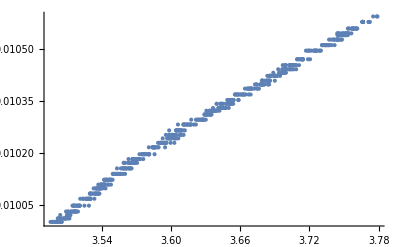

```mathematica
ListPlot[Transpose[{data⟦All,6⟧/10^6,data⟦All,7⟧/10^6}]]
```

```mathematica
(14000/10)/60.
```

23.3333

```mathematica
c33=-d0*wy*wy*(2*length-ys2)/d1/8
c34=-d0*wy*wy*ys*ys/d1/d1/2
c44=-d0*(2*length+ys2)/d1/d1/d1/8
FullSimplify[c44+c33]
c44+c33
```

-(d0 wy^2 (2 length-ys2))/(8 d1)

-(d0 wy^2 ys^2)/(2 d1^2)

-(d0 (2 length+ys2))/(8 d1^3)

-(d0 (2 length (1+d1^2 wy^2)+ys2-d1^2 wy^2 ys2))/(8 d1^3)

-(d0 wy^2 (2 length-ys2))/(8 d1)-(d0 (2 length+ys2))/(8 d1^3)

```mathematica
d⟦1;;-1;;4⟧
```

{85,54958.6,29160.4,21593.7,50216.8,26974.1,19051.6,49051.9,26088.6,15912.2,47616.1,25306.1,12727.1,48292.9,26295.3,10303.8,49666.4,26659.1,8317.46,50063.2,26873.,7311.04,51415.4,27982.9,7349.94,52929.9,28543.8,7311.11,53051.7,28652.6,7060.02,53554.3,28815.3,6483.85,52763.1,28068.8,5542.45,51995.8,28103.9,4668.33,53066.7,28553.1,3877.31,53028.5,28344.,3073.52,53303.6,28806.4,2628.01,53104.5,28827.3,2520.94,54025.6,29370.6,2420.17,56087.4,30288.2,2468.39,56672.9,30472.3,2383.57,55984.1,30123.2,2024.35,55003.4,29486.6,1796.29,55301.6,29500.,1504.64,55146.1,29547.1,1229.42,55985.9,30379.2,1127.13,57838.6,31339.,1041.42,58117.3,31380.5,1003.68,58174.6,31500.2,1047.42,58195.5,31358.5,1070.42,58060.8,31353.4,978.116,56225.8,30478.1,869.782,56473.6,30363.6,802.348,57353.9,30951.2,686.455,55614.3,29991.8,528.944,55879.9,29999.,451.116,58144.6,31085.5,470.457,57970.7,31125.7,461.161,56085.8,30515.5,430.592,56895.6,31145.8,512.85,59428.5,31906.1,599.278,59169.7,31630.,512.472,57463.,31055.9,419.265,58604.7,31602.7,396.543,59878.9,32454.,414.886,59400.2,31961.5,398.947,59885.5,32176.5,403.431,60005.2,32380.9,432.163,60089.3,32214.9,444.697,60078.3,32141.4,458.792,58239.4,31429.2,27252.,261.387,138.795,24183.7,4.05357,9.7401,23777.5,173.341,159.798,22643.1,440.706,232.597,20551.4,423.998,277.515,16955.2,717.685,444.4,13238.4,866.027,490.037,10367.5,819.648,433.718,8398.12,749.309,322.354,7706.92,371.428,165.46,7829.64,186.909,82.5597,7941.78,171.117,81.4763,7772.92,146.758,72.2411,7113.81,133.885,89.4837,6018.04,176.562,82.3212,4921.68,109.74,26.5368,4135.32,43.164,47.1248,3719.84,132.19,84.2058,3400.64,190.29,73.2578,3024.51,109.557,53.88,2925.95,61.5857,35.3567,2908.82,49.9792,32.1947,2721.38,101.477,58.8869,2406.96,119.428,56.7886,1957.05,88.9435,52.0239,1529.92,95.7081,62.9584,1376.7,94.2247,38.1272,1354.74,59.0805,24.5888,1316.71,71.4784,50.035,1246.32,142.004,74.9813,1097.48,77.4225,19.4728,934.06,30.2922,17.004,756.443,29.0518,20.6032,692.97,38.5432,20.754,681.309,27.4009,18.7382,558.516,37.1286,11.23,433.997,23.9378,14.1059,455.234,18.7419,8.49759,471.184,14.9223,3.55397,430.29,6.83792,4.74584,390.362,13.6697,7.3606,327.718,11.3727,12.8984,278.961,33.3925,21.4394,216.994,18.3864,4.78333,213.02,2.30417,0.404377,238.547,0.871604,0.0127753,228.655,1.02526,0.545977,186.098,5.63529,5.50732,159.093,13.1305,3.56691,153.924,9.05693,13.0907,133.232,41.0822,28.1371,117.041,38.6584,9.08078,85.4718}

```mathematica
d={85,29928.5581729,16115.3774777,23021.9678253,86,30163.2568342,16241.75368,23202.5052571,87,28966.5976267,15597.3987221,22281.9981744,88,28414.8596069,15300.3090191,21857.584313,89,28029.1349645,15092.6111347,21560.8730496,90,26726.8957138,14391.4053843,20559.1505491,91,25924.7766919,13959.4951418,19942.1359169,92,26157.3061581,14084.7033159,20121.004737,93,25646.9153724,13809.8775082,19728.3964403,94,23528.6825009,12669.2905774,18098.9865391,95,21547.1956605,11602.3361249,16574.7658927,96,20895.5331649,11251.4409349,16073.4870499,97,20493.0837876,11034.7374241,15763.9106059,98,18716.3506513,10078.0349661,14397.1928087,99,16714.287141,9000.00076824,12857.1439546,100,16024.2793475,8628.45811021,12326.3687289,101,15811.7606894,8514.02498658,12162.892838,102,14644.7961128,7885.65944537,11265.2277791,103,13297.824098,7160.36682201,10229.09546,104,12600.2884491,6784.77070335,9692.52957621,105,12551.1157479,6758.29309503,9654.70442148,106,12067.4674652,6497.86709663,9282.6672809,107,10982.0816814,5913.4285977,8447.75513957,108,10343.4212972,5569.53454462,7956.47792088,109,10290.1054304,5540.826001,7915.46571571,110,10095.990921,5436.3028036,7766.14686228,111,9524.61472337,5128.6386972,7326.62671029,112,9321.03236321,5019.01742634,7170.02489478,113,9332.73374209,5025.31816882,7179.02595546,114,9395.31681416,5059.01674609,7227.16678013,115,9411.46662147,5067.71279618,7239.58970882,116,9280.95837747,4997.43912633,7139.1987519,117,9284.32793958,4999.25350593,7141.79072275,118,9476.85052522,5102.91951358,7289.8850194,119,9438.92635925,5082.49880883,7260.71258404,120,9377.75082761,5049.55813794,7213.65448277,121,9306.76088322,5011.33278327,7159.04683324,122,9104.80092929,4902.58511577,7003.69302253,123,8993.00727156,4842.38853084,6917.6979012,124,9004.13512115,4848.38044985,6926.2577855,125,8991.28439886,4841.46083016,6916.37261451,126,8532.8265654,4594.59891983,6563.71274262,127,8275.1472246,4455.84850555,6365.49786508,128,8357.09699818,4499.97530671,6428.53615244,129,8312.26655949,4475.83583973,6394.05119961,130,7912.53448101,4260.59548978,6086.56498539,131,7612.6552103,4099.12203632,5855.88862331,132,7774.81815672,4186.44054593,5980.62935133,133,7713.38328932,4153.36023271,5933.37176102,134,7301.13374631,3931.37970955,5616.25672793,135,6729.37205044,3623.50802716,5176.4400388,136,6439.6459699,3467.5016761,4953.573823,137,6388.14146242,3439.76847977,4913.95497109,138,6031.06860438,3247.49847928,4639.28354183,139,5383.11650383,2898.60119437,4140.8588491,140,4959.71636184,2670.61650253,3815.16643219,141,4855.45490143,2614.47571615,3734.96530879,142,4675.16709222,2517.39766504,3596.28237863,143,4306.79804211,2319.0450996,3312.92157086,144,4072.81186983,2193.05254529,3132.93220756,145,4040.8005448,2175.81567797,3108.30811138,146,3914.87386337,2108.00900335,3011.44143336,147,3539.00597726,1905.61860314,2722.3122902,148,3346.87845742,1802.16532323,2574.52189032,149,3324.20234717,1789.95511001,2557.07872859,150,3293.54801427,1773.44893076,2533.49847251,151,3196.15116988,1721.00447609,2458.57782299,152,3196.52057199,1721.20338492,2458.86197845,153,3184.6323399,1714.80202918,2449.71718454,154,3188.2706328,1716.76110997,2452.51587139,155,3355.02296549,1806.55082757,2580.78689653,156,3465.71000595,1866.15154166,2665.9307738,157,3503.87480828,1886.70181984,2695.28831406,158,3401.20814906,1831.41977257,2616.31396082,159,3426.75161976,1845.1739491,2635.96278443,160,3513.10480199,1891.67181646,2702.38830922,161,3535.33221073,1903.64042116,2719.48631595,162,3397.74709544,1829.55612831,2613.65161187,163,3157.97439952,1700.44775359,2429.21107655,164,3087.22071423,1662.34961535,2374.78516479,165,3090.19649153,1663.95195698,2377.07422426,166,3043.66815694,1638.89823835,2341.28319765,167,2862.40775422,1541.29648304,2201.85211863,168,2752.25950276,1481.9858861,2117.12269443,169,2770.95283282,1492.05152537,2131.5021791,170,2631.27756693,1416.84176681,2024.05966687,171,2551.70503587,1373.99501932,1962.85002759,172,2509.18516501,1351.09970424,1930.14243463,173,2517.39093863,1355.51819773,1936.45456818,174,2363.21202272,1272.49878147,1817.85540209,175,2133.81690757,1148.97833484,1641.39762121,176,1996.10227918,1074.82430417,1535.46329168,177,1940.14585563,1044.69392226,1492.41988894,178,1889.74783201,1017.55652493,1453.65217847,179,1726.87210471,929.85421023,1328.36315747,180,1622.67830661,873.749857406,1248.21408201,181,1589.31029901,855.782468699,1222.54638386,182,1589.34431701,855.800786081,1222.57255154,183,1625.73522667,875.395891284,1250.56555898,184,1574.13482019,847.611057023,1210.8729386,185,1539.6417664,829.037874216,1184.33982031,186,1573.09484371,847.051069689,1210.0729567,187,1559.22964501,839.585193465,1199.40741924,188,1482.89070575,798.479610789,1140.68515827,189,1504.01557743,809.854541694,1156.93505956,190,1485.97226129,800.138909926,1143.05558561,191,1341.02578904,722.090809486,1031.55829927,192,1293.34873018,696.418547019,994.883638598,193,1329.85309065,716.07474112,1022.96391589,194,1286.27218982,692.608102211,989.440146016,195,1291.44250596,695.392118595,993.417312278,196,1294.28953004,696.925131563,995.607330804,197,1285.3298171,692.100670744,988.71524392,198,1246.59948897,671.245878679,958.922683827,199,1210.12516428,651.605857687,930.865510982,200,1258.21224639,677.498901901,967.855574144,201,1261.33025217,679.177828094,970.254040134,202,1246.93670758,671.427457929,959.182082756,203,1117.90792421,601.950420729,859.92917247,204,1143.04597668,615.486295137,879.266135909,205,1153.98921146,621.37880617,887.684008814,206,1146.53456605,617.364766337,881.949666195,207,1118.13585771,602.073154153,860.104505933,208,1056.0126312,568.62218603,812.317408615,209,1007.40195047,542.447204102,774.924577288,210,996.916043519,536.80094651,766.858495015,211,1003.74703294,540.479171581,772.113102258,212,901.545954168,485.447821475,693.496887822,213,863.064390483,464.726979491,663.895684987,214,842.29086568,453.541235366,647.916050523,215,741.997114455,399.536907784,570.767011119,216,706.768357909,380.567577336,543.667967622,217,739.704584155,398.302468391,569.003526273,218,720.233568897,387.81807556,554.025822229,219,655.801707056,353.123996107,504.462851582,220,627.560730798,337.917316584,482.739023691,221,632.750481169,340.711797553,486.731139361,222,632.510786016,340.582730932,486.546758474,223,652.720018104,351.464625133,502.092321618,224,617.52552867,332.513746207,475.019637438,225,574.480826127,309.335829453,441.90832779,226,557.032277786,299.940457269,428.486367528,227,570.72729066,307.314694971,439.020992815,228,662.052204392,356.489648519,509.270926456,229,692.485271046,372.87668441,532.680977728,230,687.46124742,370.171440918,528.816344169,231,666.00589735,358.618560112,512.312228731,232,683.950289665,368.280925204,526.115607435,233,732.271744786,394.300170269,563.285957527,234,754.33650168,406.181193212,580.258847446,235,710.813773793,382.745878196,546.779825995,236,626.91196613,337.567981762,482.239973946,237,641.338832958,345.33629467,493.337563814,238,652.14489091,351.154941259,501.649916085,239,660.053251926,355.413289499,507.733270712,240,666.786164392,359.038703903,512.912434147,241,651.373769783,350.739722191,501.056745987,242,632.247270514,340.440837969,486.344054242,243,630.860938368,339.694351429,485.277644898,244,655.627474896,353.03017879,504.328826843,245,684.50986166,368.582233202,526.546047431,246,688.284502217,370.614731963,529.44961709,247,652.962707857,351.59530423,502.279006044,248,655.833418877,353.141071703,504.48724529,249,740.694816472,398.835670408,569.76524344,250,766.581429349,412.774615803,589.678022576,251,751.048701446,404.41083924,577.729770343,252,736.131695318,396.378605171,566.255150244,253,686.805162479,369.818164412,528.311663446,254,684.982951056,368.836973645,526.90996235,255,675.571314247,363.76916921,519.670241728,256,641.157525977,345.238667834,493.198096906,257,609.021356974,327.934576832,468.477966903,258,597.782976693,321.883141296,459.833058995,259,604.270866676,325.376620518,464.823743597,260,573.637827536,308.881907135,441.259867335,261,614.558557489,330.91614634,472.737351914,262,607.947223906,327.356197488,467.651710697,263,601.702758511,323.993793044,462.848275778,264,583.209632346,314.035955879,448.622794112,265,530.05961174,285.416714014,407.738162877,266,524.714878434,282.538780695,403.626829565,267,505.180138822,272.02007475,388.600106786,268,493.654835442,265.814142161,379.734488802,269,461.438498789,248.466883963,354.952691376,270,452.870930007,243.853577696,348.362253852,271,454.406437228,244.680389276,349.543413252,272,470.584755379,253.391791358,361.988273368,273,528.386639503,284.515882809,406.451261156,274,539.129124216,290.300297655,414.714710936,275,550.433818033,296.387440479,423.410629256,276,597.272209167,321.608112628,459.440160898,277,644.583310834,347.083321218,495.833316026,278,651.48880597,350.801664753,501.145235361,279,652.555369648,351.375968272,501.96566896,280,645.023181182,347.320174483,496.171677832,281,626.169717007,337.168309157,481.669013082,282,640.229535827,344.73898083,492.484258328,283,617.595863499,332.551618807,475.073741153,297,35309.2005903,19012.6464717,27160.923531,298,35227.2222329,18968.5042793,27097.8632561,299,32904.6955411,17717.9129837,25311.3042624,300,30904.1233694,16640.6818143,23772.4025918,301,31414.661453,16915.5869362,24165.1241946,302,32823.8640036,17674.3883096,25249.1261566,303,32568.5109088,17536.8904894,25052.7006991,304,31555.7838486,16991.5759185,24273.6798835,305,32347.8338921,17418.0644034,24882.9491478,306,32960.4944169,17747.9585322,25354.2264746,307,31378.0271468,16895.8607714,24136.9439591,308,30348.7539297,16341.6367314,23345.1953305,309,30318.0232013,16325.0894161,23321.5563087,310,28856.0156208,15537.8545651,22196.935093,311,27295.5447865,14697.6010389,20996.5729127,312,26966.3253619,14520.329041,20743.3272014,313,26068.0879842,14036.6627607,20052.3753725,314,23973.0596986,12908.570607,18440.8151528,315,22556.6719389,12145.9002748,17351.2861069,316,22376.3206722,12048.7880543,17212.5543632,317,21592.9820113,11626.9903138,16609.9861625,318,19541.8427652,10522.5307197,15032.1867425,319,18071.4996269,9730.80749142,13901.1535592,320,17850.0097573,9611.54371547,13730.7767364,321,17363.5757477,9349.61771032,13356.596729,322,16078.2068845,8657.49601474,12367.8514496,323,14731.1968341,7932.18291066,11331.6898724,324,14242.9800454,7669.29694754,10956.1384965,325,14068.8752547,7575.54821409,10822.2117344,326,13348.0730409,7187.4239451,10267.748493,327,12205.3143344,6572.09233392,9388.70333418,328,11635.0377862,6265.02034639,8950.02906627,329,11702.704809,6301.45643561,9002.0806223,330,11267.7467872,6067.24827004,8667.49752863,331,10433.4689877,5618.0217626,8025.74537515,332,10049.9641851,5411.51917659,7730.74168084,333,10301.5896144,5547.00979239,7924.29970341,334,10482.3933549,5644.36565262,8063.37950374,335,10388.0197221,5593.54908114,7990.78440162,336,10346.7495778,5571.32669573,7959.03813675,337,10536.5843963,5673.54544419,8105.06492027,338,10823.5403267,5828.06017589,8325.80025127,339,11040.5302784,5944.90091912,8492.71559874,340,11144.1093939,6000.67428902,8572.39184146,341,11014.9537132,5931.12892248,8473.04131782,342,10952.6633079,5897.58793505,8425.1256215,343,10933.1812732,5887.09760865,8410.13944093,344,11004.3253109,5925.40593665,8464.86562378,345,10695.5071906,5759.11925646,8227.31322351,346,10016.1619065,5393.31794964,7704.73992806,347,9560.16565042,5147.78150407,7353.97357724,348,9530.87661754,5132.01048637,7331.44355195,349,9360.07486019,5040.04030933,7200.05758476,350,8651.96161525,4658.74856206,6655.35508865,351,8245.91109411,4440.10597375,6343.00853393,352,8118.17005885,4371.32233938,6244.74619912,353,7907.55539167,4257.91444167,6082.73491667,354,7429.82343017,4000.67415471,5715.24879244,355,7051.34725407,3796.87929065,5424.11327236,356,6941.61992811,3737.7953459,5339.70763701,357,6763.9247041,3642.11330221,5203.01900315,358,6299.66254089,3392.12598356,4845.89426222,359,5673.10280241,3054.74766283,4363.92523262,360,5433.30479143,2925.62565693,4179.46522418,361,5423.50302995,2920.34778536,4171.92540766,362,5171.81389548,2784.8228668,3978.31838114,363,4867.46684761,2620.94368717,3744.20526739,364,4775.28048501,2571.30487654,3673.29268077,365,4756.23608222,2561.05019812,3658.64314017,366,4621.5256049,2488.51378726,3555.01969608,367,4473.54585161,2408.83238163,3441.18911662,368,4401.43521693,2370.00357834,3385.71939764,369,4414.8020414,2377.20109922,3396.00157031,370,4342.3726045,2338.20063319,3340.28661885,371,4040.5258941,2175.66778913,3108.09684162,372,3949.33529234,2126.56515741,3037.95022488,373,3963.4753304,2134.17902406,3048.82717723,374,3901.72508432,2100.92889156,3001.32698794,375,3815.79189524,2054.65717436,2935.2245348,376,3823.06707182,2058.57457714,2940.82082448,377,3787.30565623,2039.31843028,2913.31204326,378,3698.87368849,1991.70121688,2845.28745269,379,3705.14057386,1995.07569362,2850.10813374,380,3712.09754965,1998.82175751,2855.45965358,381,3630.0347365,1954.63408888,2792.33441269,382,3524.41750817,1897.76327363,2711.0903909,383,3518.62716595,1894.64539705,2706.6362815,384,3540.68212025,1906.52114167,2723.60163096,385,3455.06183486,1860.41791108,2657.73987297,386,3269.46538143,1760.48135923,2514.97337033,387,3191.27344762,1718.37801026,2454.82572894,388,3155.78985714,1699.27146154,2427.53065934,389,3110.56254472,1674.91829331,2392.74041901,390,2955.65475175,1591.50640479,2273.58057827,391,2732.09238652,1471.12666966,2101.60952809,392,2726.45597032,1468.09167632,2097.27382332,393,2649.51259407,1426.66062758,2038.08661083,394,2414.1797482,1299.94294134,1857.06134477,395,2228.63311708,1200.03321689,1714.33316698,396,2197.14104362,1183.07594656,1690.10849509,397,2150.76876139,1158.10625614,1654.43750877,398,1977.84824308,1064.99520781,1521.42172544,399,1825.24789511,982.825789673,1404.03684239,400,1734.64222314,934.03812015,1334.34017164,401,1746.76978555,940.568346067,1343.66906581,402,1691.53281747,910.825363253,1301.17909036,403,1584.10612333,852.980220252,1218.54317179,404,1540.75461681,829.637101361,1185.19585909,405,1568.44801047,844.548928717,1206.4984696,406,1587.28325212,854.69098191,1220.98711701,407,1542.37520626,830.509726449,1186.44246636,408,1508.81203238,812.437248206,1160.62464029,409,1527.96766162,822.751817797,1175.35973971,410,1577.33680854,849.335204599,1213.33600657,411,1527.15062225,822.311873521,1174.73124789,412,1521.54185384,819.291767452,1170.41681065,413,1519.65664923,818.276657277,1168.96665325,414,1454.54653677,783.217365955,1118.88195136,415,1465.18511531,788.945831318,1127.06547331,416,1488.59073793,801.548858886,1145.06979841,417,1466.37875616,789.588561011,1127.98365859,418,1396.43134873,751.924572391,1074.17796056,419,1444.86183465,778.00252635,1111.4321805,420,1477.04008042,795.329274073,1136.18467725,421,1384.86415725,745.696084674,1065.28012096,422,1235.48816969,665.262860601,950.375515144,423,1148.2257306,618.275393399,883.250561998,424,1140.04206221,613.868802726,876.955432465,425,1077.07467333,579.963285639,828.518979484,426,1011.86650529,544.851195158,778.358850226,427,940.715907186,506.539334639,723.627620912,428,891.518157796,480.048238813,685.783198305,429,902.721527278,486.08082238,694.401174829,430,885.37995635,476.743053419,681.061504885,431,836.783567531,450.575767132,643.679667331,432,818.262179638,440.602712113,629.432445875,433,796.407954033,428.835052172,612.621503102,434,714.407927688,384.681191832,549.54455976,435,637.720614782,343.388023344,490.554319063,436,649.713573373,349.845770278,499.779671825,437,631.725033196,340.15963326,485.942333228,438,608.272036696,327.531096683,467.901566689,439,579.721601657,312.157785507,445.939693582,440,569.156511003,306.46889054,437.812700772,441,601.22597509,323.73706351,462.4815193,442,650.210070365,350.113114812,500.161592588,443,668.952824026,360.205366783,514.579095404,444,656.630839013,353.570451776,505.100645394,445,692.105520177,372.672203172,532.388861675,446,720.330339812,387.870182976,554.100261394,447,701.379223957,377.665735977,539.522479967,448,699.447195302,376.625412855,538.036304078,449,665.410721984,358.298081068,511.854401526,450,638.848392413,343.995288223,491.421840318,451,641.544703974,345.447148293,493.495926133,452,645.257077327,347.446118561,496.351597944,453,623.443910648,335.700567272,479.57223896,454,564.972178137,304.215788228,434.593983182,455,538.366238016,289.889512778,414.127875397,456,525.698185526,283.068253745,404.383219635,457,515.466872239,277.559085052,396.512978645,458,445.091042875,239.664407702,342.377725288,459,386.380615349,208.051100572,297.215857961,460,376.533679315,202.748904247,289.641291781,461,365.949330585,197.049639546,281.499485066,462,324.753855605,174.86746071,249.810658157,463,316.779782477,170.573729026,243.676755751,464,325.436157736,175.234854165,250.335505951,465,332.411781325,178.990959175,255.70137025,466,324.984048871,174.991410931,249.987729901,467,319.072771937,171.808415658,245.440593798,468,328.862729021,177.079931011,252.971330016,469,313.815225843,168.9774293,241.396327571,470,305.677530953,164.59559359,235.136562272,471,298.488372623,160.724508335,229.606440479,472,295.496134313,159.113303092,227.304718702,473,272.035422493,146.480612112,209.258017302,474,246.921731348,132.957855341,189.939793344,475,243.165313321,130.935168711,187.050241016,476,237.736864268,128.012157683,182.874510975,477,237.293196706,127.773259765,182.533228235,478,228.874149981,123.239926913,176.057038447,479,206.127486003,110.991723232,158.559604618,480,193.819449441,104.36431893,149.091884185,481,200.093925574,107.742883002,153.918404288,482,223.679399548,120.442753603,172.061076576,483,239.073167727,128.731705699,183.902436713,484,242.303417811,130.471071129,186.38724447,485,247.64421164,133.346883191,190.495547415,486,242.074470134,130.347791611,186.211130872,487,219.582691683,118.236833983,168.909762833,488,213.63418326,115.033790986,164.333987123,489,208.229412293,112.123529696,160.176470994,490,178.952690894,96.3591412508,137.655916073,491,161.334257437,86.8722924663,124.103274952,492,157.262718698,84.6799254527,120.971322075,493,145.98300015,78.6062308498,112.2946155,494,139.009077643,74.851041808,106.930059726,495,150.609299495,81.0973151125,115.853307304,496,158.33915794,85.2595465828,121.799352261,497,148.489090229,79.9556639693,114.222377099,498,128.563886161,69.2267079327,98.8952970467,499,107.920235613,58.1108960993,83.0155658562,500,101.033044824,54.4024087516,77.717726788,501,95.5615261985,51.4562064146,73.5088663065,502,82.4154056232,44.3775261048,63.396465864,503,81.4917927395,43.8801960905,62.685994415,504,76.8503936894,41.3809812174,59.1156874534,505,79.9821629228,43.0673184969,61.5247407099,506,105.059211484,56.5703446454,80.8147780648
};
```

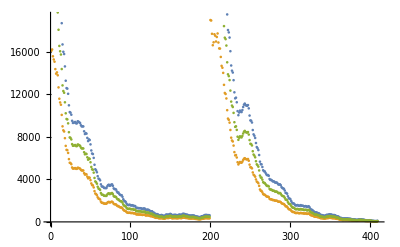

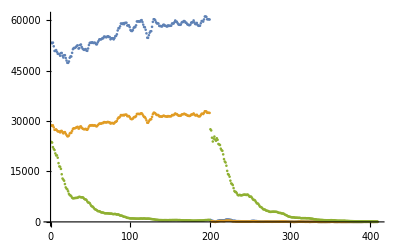

```mathematica
ListPlot[{d⟦2;;-1;;4⟧,d⟦3;;-1;;4⟧,d⟦4;;-1;;4⟧}]
ListPlot[{d2⟦2;;-1;;4⟧,d2⟦3;;-1;;4⟧,d2⟦4;;-1;;4⟧}]
```

```mathematica
d2={85,53325.9853667,28713.9921205,23784.1252101,86,53147.4362049,28617.8502642,23600.7670246,87,53353.0261962,28728.5525672,22247.4990812,88,52254.9443033,28137.2777018,21707.9850585,89,50874.8381165,27394.1436012,21392.5798624,90,50889.1153997,27401.8313691,20376.0362875,91,51133.3919788,27533.3649116,19778.2936074,92,50594.2641089,27243.0652894,19799.2043068,93,50026.5880384,26937.3935591,19100.9069231,94,50037.0841205,26943.0452956,17486.3384755,95,49915.8360497,26877.7578729,16503.9716229,96,49442.2111479,26622.7290796,16401.6376142,97,50228.4649742,27046.0965246,15771.0808436,98,50269.8970346,27068.4060956,14176.1920657,99,49441.6044168,26622.4023783,12900.7627212,100,48912.1534975,26337.3134217,12582.9338371,101,49577.982329,26695.8366387,12237.3327407,102,49607.5901621,26711.7793181,11260.529168,103,48765.3585687,26258.2699985,10275.8678195,104,48007.9213293,25850.4191773,9902.74758702,105,47344.3407748,25493.106571,9675.75409349,106,47326.5105795,25483.5056966,9108.61329309,107,47743.0159116,25707.7777985,8352.47546598,108,48850.1547351,26303.9294728,7969.94842081,109,49250.7216202,26519.6193339,7884.02073338,110,49209.1187275,26497.2177763,7607.44905278,111,50308.8878049,27089.4011257,7190.06102802,112,51386.1577256,27669.4695445,7001.22248949,113,51746.2182756,27863.3483023,7066.35351315,114,51725.9499993,27852.434615,7071.59421814,115,51847.2237863,27917.735885,7116.53235864,116,52089.2707033,28048.0688402,7141.1379699,117,52405.8286865,28218.5231389,7144.74103368,118,52527.3354425,28283.9498537,7209.16123551,119,51582.2354631,27775.0498648,7373.69608314,120,51702.6215421,27839.8731381,7464.63293726,121,52633.0989185,28340.8994176,7406.21219016,122,52783.2969634,28421.775288,7339.4600871,123,52060.4410427,28032.5451769,7288.552262,124,51579.5447583,27773.6010237,7324.56864827,125,51343.4772316,27646.4877401,7216.96296821,126,51184.5358873,27560.9039393,6890.19748308,127,51299.097178,27622.5907881,6697.70470481,128,51419.0093561,27687.158884,6690.02027229,129,50955.2695192,27437.452818,6521.15305696,130,50901.1229389,27408.2969671,6074.50556511,131,51600.5635894,27784.9188559,5764.41452328,132,52628.9200143,28338.6492385,5743.32127869,133,53234.7439612,28664.8621329,5589.47224386,134,53355.7818747,28730.0363941,5161.09165834,135,53277.7508032,28688.0196632,4746.58861006,136,53461.1096825,28786.7513675,4591.14552983,137,53271.56832,28684.6906338,4495.43675483,138,53237.1619935,28666.1641504,4191.47618136,139,53354.9360763,28729.5809641,3861.34294156,140,53232.7114568,28663.7677075,3704.11947792,141,52856.9232631,28461.4202186,3629.20180263,142,52841.0213997,28452.8576768,3451.97232789,143,53395.1875813,28751.2548515,3231.23145608,144,53824.6411899,28982.4991023,3184.44099497,145,54295.7289489,29236.1617417,3172.65673885,146,54338.041096,29258.9452055,3076.70993507,147,54298.2531444,29237.5209239,2878.01178548,148,54421.7217853,29304.0040382,2796.01292708,149,54707.5690486,29457.9217954,2801.46771051,150,54632.5584545,29417.5314755,2750.30488831,151,55157.7534471,29700.3287792,2646.9364742,152,55095.5268263,29666.8221372,2552.48405465,153,55000.8525178,29615.8436634,2557.13013588,154,54933.7886139,29579.7323306,2548.86974254,155,55180.2984057,29712.4683723,2542.12324623,156,55242.6249499,29746.0288192,2534.13727379,157,55008.3060831,29619.8571217,2504.90829966,158,55024.3134113,29628.4764523,2469.11390592,159,54330.4462176,29254.8556556,2463.32137526,160,54639.8609685,29421.4635984,2472.49476228,161,54592.8783523,29396.1652666,2406.40881483,162,54668.9552865,29437.1297696,2316.387919,163,54308.2203425,29242.8878767,2318.94753274,164,54679.1850251,29442.6380904,2353.00495688,165,55251.9030315,29751.0247092,2369.4929102,166,55351.5625175,29804.6875094,2261.44204317,167,55829.8808786,30062.24355,2180.28404282,168,56961.1975607,30671.4140711,2223.75719841,169,57648.0389312,31041.2517322,2220.78003548,170,57629.5601845,31031.3016378,2056.91476953,171,58201.3723879,31339.2005166,1897.42632943,172,59034.6461126,31787.8863683,1888.38963351,173,58985.1065724,31761.2112313,1856.29176682,174,58887.6559645,31708.737827,1760.30236223,175,59139.4844723,31844.3377928,1614.9933593,176,58817.6634916,31671.0495724,1519.19227198,177,59210.372527,31882.5082837,1500.96233265,178,59215.5361211,31885.2886806,1438.01286179,179,59257.4813028,31907.8745477,1311.97589038,180,58421.9573997,31457.9770614,1204.8185014,181,58470.9052361,31484.3335886,1187.71878363,182,58502.6286944,31501.4154508,1147.77906381,183,57966.2672072,31212.6054193,1064.25024207,184,57077.3460602,30733.9555709,1032.25160395,185,56833.9593953,30602.9012129,1021.20570882,186,56795.673415,30582.285685,1040.95369526,187,57082.5174911,30736.7401875,1018.82568806,188,57717.2542193,31078.5215027,1011.69549983,189,58009.8738574,31236.0859232,1007.06708768,190,57943.6887479,31200.4477874,983.224128481,191,58488.461125,31493.7867596,970.436287032,192,59648.4334109,32118.3872213,963.798047473,193,59648.4334109,32118.3872213,970.167665489,194,59690.6952025,32141.1435706,958.176964387,195,59606.0458013,32095.5631238,962.003672789,196,59606.0458013,32095.5631238,993.061939641,197,59951.4909388,32281.572044,1011.65197375,198,60042.9483846,32330.8183609,1007.52722124,199,59460.3047851,32017.087192,971.281358107,200,58688.4160427,31601.4547922,1002.41224647,201,57997.5081926,31229.4274883,1028.9671278,202,57916.2805224,31185.6895121,1000.35104183,203,57175.992897,30787.0730984,961.614300571,204,56104.7818475,30210.2671487,959.8044084,205,54813.4543612,29514.9369637,972.482000256,206,54765.966891,29489.3667875,970.252642604,207,55544.3947715,29908.5202616,967.237362884,208,56297.0857376,30313.8153972,937.126829742,209,56725.116299,30544.2933918,893.32544379,210,56747.169388,30556.168132,867.670989643,211,58050.0361802,31257.7117893,821.677543002,212,59529.8958782,32054.5593191,799.825146162,213,60309.0961745,32474.1287094,767.979615839,214,60296.8824748,32467.5521018,731.064101275,215,59995.1726577,32305.0929695,677.142354295,216,59411.8479938,31990.9950736,631.622057894,217,59071.9334157,31807.9641469,633.62966795,218,59075.9693207,31810.1373265,597.325104821,219,59033.2590398,31787.139483,567.680098094,220,58326.3910971,31406.5182831,538.025677124,221,58278.2229933,31380.5816118,544.747889155,222,58298.9324421,31391.7328535,533.41840663,223,58130.0433762,31300.7925872,526.786078684,224,58257.9970574,31369.6907232,516.358513872,225,58645.7300073,31578.470004,513.418638274,226,58668.8215141,31590.9038922,520.553548652,227,58375.1503848,31432.7732841,535.78180264,228,58375.1503848,31432.7732841,523.499894312,229,58180.5016666,31327.9624359,523.138619692,230,58152.4481879,31312.8567165,518.639093994,231,58489.4127298,31494.2991622,504.368258965,232,58297.1604875,31390.7787241,521.670304515,233,58393.9645347,31442.9039802,540.607397475,234,58351.5338493,31420.0566881,536.817873783,235,58393.9882602,31442.9167555,534.188159769,236,59036.8149825,31789.0542214,553.66258482,237,59036.8149825,31789.0542214,553.593442693,238,59032.7912003,31786.8875694,547.7704287,239,59418.9437751,31994.8158789,554.367950861,240,59937.5474095,32274.0639897,561.157167041,241,59549.7801712,32065.2662461,563.228143114,242,59568.1289924,32075.1463805,564.288138523,243,59138.4977916,31843.8065032,544.90143633,244,58752.0310286,31635.7090154,519.814239158,245,58655.4924634,31583.726711,541.366447105,246,58643.7776454,31577.4187321,533.696627236,247,58729.2713743,31623.4538169,498.447145736,248,59309.4484504,31935.8568579,478.177166677,249,59503.2664345,32040.2203878,473.723975737,250,59484.1984945,32029.9530355,463.010867557,251,59786.9875098,32192.9932745,437.752629317,252,59657.262394,32123.1412891,455.821437327,253,59271.5906061,31915.4718648,463.063057801,254,59261.6979198,31910.1450337,457.658039194,255,58829.4222991,31677.381238,451.442622616,256,58700.7378071,31608.0895885,444.836221412,257,58557.0685159,31530.7292008,450.732637049,258,58543.6733992,31523.5164457,452.587842896,259,58716.3595552,31616.5012989,430.025883435,260,59296.777437,31929.0340046,396.057058102,261,59392.7714449,31980.7230857,377.48460689,262,59377.0722436,31972.2696696,372.918635491,263,59946.7525392,32279.020598,366.809519681,264,59362.9622419,31964.6719764,374.646055344,265,58887.9026532,31708.8706594,381.147246607,266,58856.687384,31692.0624375,376.643038446,267,59211.2266821,31882.9682134,389.159720677,268,58630.7476295,31570.4025697,406.18566035,269,58350.854991,31419.691149,402.544017156,270,58343.133433,31415.533387,410.907075956,271,58387.509899,31439.4284071,419.479547175,272,59095.9989604,31820.9225171,426.839770717,273,59753.1585583,32174.7776853,415.552106047,274,59777.071098,32187.6536682,426.059350936,275,59599.8771269,32092.2415299,437.871106512,276,60250.1656451,32442.3968858,468.214873715,277,61115.1520869,32908.158816,516.731714342,278,61132.3135559,32917.399607,533.036852686,279,60999.4892541,32845.8788291,531.216254187,280,60280.2443484,32458.5931107,552.720706596,281,60328.509865,32484.582235,587.247870173,282,60271.9105333,32454.1056718,586.264683224,283,60227.456614,32430.168946,559.233770403,297,598.112610125,322.060636221,27564.8950104,298,399.891755799,215.326330046,27216.3794175,299,305.149732221,164.311394273,25056.4848757,300,305.520678995,164.511134843,23926.3866288,301,203.585529,109.622977154,24781.6498592,302,61.1819415977,32.9441223988,25389.2944729,303,7.13362023263,3.84118012526,24493.4022722,304,42.3510413425,22.8044068768,24141.0937215,305,189.216389702,101.885748301,24894.3558629,306,335.860882836,180.848167681,24430.9017331,307,337.411166593,181.682935858,23184.9348723,308,397.043024511,213.792397814,23044.0531591,309,498.090875601,268.20277917,22872.7456038,310,481.84941221,259.457375805,21789.0097938,311,495.552225031,266.835813478,21326.520192,312,476.505804521,256.580048588,21153.3606052,313,442.750451029,238.404089016,20095.3811647,314,417.758839326,224.94706733,18678.8099189,315,446.863950749,240.619050403,17965.9503065,316,632.442649456,340.546042015,17679.9907896,317,689.173303674,371.093317363,16719.1656676,318,703.154151973,378.621466447,15184.6019572,319,684.220639164,368.426498011,14229.3531354,320,684.220639164,368.426498011,14013.7982406,321,645.332822986,347.486904685,13451.7715419,322,595.954986093,320.898838665,12269.8551289,323,585.437563036,315.235610865,11459.8290737,324,441.854690912,237.921756645,11284.4099974,325,339.369805321,182.73758748,10958.8278919,326,321.283220101,172.998656977,10053.9749687,327,339.885615821,183.015331596,9176.54534848,328,312.091126934,168.049068349,8916.06206258,329,234.104171145,126.056092155,8905.38511521,330,232.723858139,125.31284669,8543.96055251,331,212.854450929,114.613935116,8060.16193875,332,224.344441218,120.800852964,7895.81592033,333,211.156272761,113.699531487,8002.29000738,334,208.319968816,112.172290901,8031.13228246,335,180.651728772,97.2740078003,7896.54105374,336,141.995358599,76.4590392459,7912.44687043,337,168.866380427,90.9280509993,7975.56767661,338,179.700717895,96.7619250203,8052.51495913,339,176.171531361,94.8615938098,8092.10054908,340,160.816736028,86.5936270922,8122.85447015,341,130.387260774,70.2085250323,8060.82314488,342,124.225167807,66.8904749728,8012.23059343,343,134.342897181,72.3384830973,8127.46177352,344,165.436077347,89.0809647254,8083.22125053,345,171.489154836,92.3403141426,7792.62626693,346,170.512606166,91.8144802434,7478.57642751,347,189.087205729,101.8161877,7537.55663939,348,250.980897139,135.143559998,7506.46662717,349,298.641673334,160.807054872,7178.25313226,350,303.059607861,163.185942695,6754.48839804,351,312.677720132,168.364926225,6545.88460086,352,303.597063931,163.475342117,6532.28989413,353,251.817908087,135.594258201,6336.15641437,354,244.589601223,131.702092966,5930.21724172,355,238.960462904,128.671018487,5537.66764332,356,134.762119545,72.5642182168,5485.22080463,357,102.450634248,55.1657261337,5352.67015766,358,102.450634248,55.1657261337,4933.24908879,359,81.9852371835,44.145896945,4548.03590192,360,48.0064005609,25.849600302,4428.50455648,361,59.8340892936,32.2183557735,4338.30772224,362,64.7193433457,34.8488771861,4062.1157218,363,57.2248191488,30.8133641571,3772.41896165,364,66.7467740525,35.9405706436,3709.87714666,365,98.4814935776,53.0284965418,3692.10690152,366,107.837889937,58.0665561199,3518.98214491,367,109.156118489,58.7763714938,3333.981685,368,121.559748411,65.4552491441,3293.77863104,369,85.6282452165,46.1075166551,3257.49587064,370,92.6276537313,49.8764289322,3132.89253449,371,94.0372336292,50.6354334927,3006.3432489,372,89.569337392,48.2296432111,2977.69429668,373,65.095920723,35.0516496201,2991.21595215,374,68.0983031952,36.6683171051,3013.99362571,375,65.9200735595,35.4954242243,3031.18041888,376,79.5529652199,42.8362120415,3036.57047845,377,93.8710289324,50.5459386559,3031.32059336,378,79.0828673471,42.5830824177,3017.14303279,379,84.5169648452,45.5091349167,3004.47687409,380,91.7139248832,49.3844210909,2982.00220773,381,98.5255200852,53.0522031228,2893.2687352,382,92.7015563298,49.9162226391,2746.58337341,383,109.466882312,58.9437058605,2680.6370023,384,139.00059745,74.8464755498,2676.14766417,385,172.191649467,92.7185804822,2643.63305731,386,181.425956852,97.6908998435,2526.59941325,387,188.82150838,101.673119897,2495.23434231,388,164.804239245,88.7407442087,2496.82589652,389,161.889226681,87.1711220591,2387.24866857,390,164.493386206,88.5733618032,2195.58773381,391,144.579254075,77.8503675787,2058.70554577,392,99.8286844221,53.7539069965,2004.81974472,393,65.588867256,35.3170823686,1846.40012577,394,64.7104666721,34.8440974388,1682.76502499,395,57.6149007903,31.0234081178,1585.2838436,396,44.3520051519,23.8818489279,1544.54917753,397,37.5630954868,20.2262821852,1485.43704883,398,31.6856193516,17.0614873432,1407.0379364,399,30.8741092424,16.6245203613,1355.65036911,400,24.2855664022,13.0768434473,1346.80107481,401,13.0337819047,7.0181902564,1353.64763314,402,4.98630665482,2.6849343526,1317.5776126,403,15.7328434454,8.47153108598,1259.56590246,404,38.1338891021,20.5336325934,1243.74837389,405,31.6760965254,17.0563596675,1257.57685669,406,40.8546854278,21.9986767688,1226.94101993,407,101.306840914,54.5498374155,1201.99327323,408,124.249413294,66.9035302353,1210.27656295,409,126.895913207,68.3285686499,1207.47418184,410,122.449231771,65.934201723,1126.47490665,411,81.7157737807,44.0008012666,1097.24069842,412,67.3834181755,36.2833790176,1115.06571798,413,79.6986012679,42.9146314519,1120.32898938,414,73.246780848,39.4405743028,1109.13877932,415,47.0389439488,25.3286621263,1118.29102469,416,40.2257887962,21.6600401211,1116.13313196,417,43.199855128,23.2614604535,1071.78816554,418,44.2112120786,23.8060372731,1081.15921433,419,45.0361002828,24.2502078446,1096.48489004,420,43.3461895896,23.3402559329,1090.42482867,421,19.4649967217,10.4811520809,1054.31888544,422,21.4218601152,11.5348477543,1001.05877035,423,38.6077899826,20.7888099907,969.178679181,424,43.2589088961,23.2932586364,946.617278168,425,45.3406765655,24.4142104584,915.045530924,426,50.5602937761,27.2247735718,840.468325364,427,56.1235815873,30.2203900854,798.463755958,428,61.5423102715,33.1381670693,779.734072941,429,71.8498436773,38.6883773647,750.240409655,430,71.8498436773,38.6883773647,683.927228762,431,30.1923247365,16.2574056274,644.096043499,432,8.83778586452,4.7588077732,650.796532179,433,3.95183339882,2.12791029167,628.207968465,434,2.75413387093,1.48299516127,599.912257712,435,1.09189316547,0.587942473713,582.559945018,436,0.598983586541,0.322529623522,574.975462273,437,1.31559167995,0.708395519975,564.954175066,438,1.81667951883,0.9782120486,547.71063788,439,0.264961981381,0.142671836128,516.159034457,440,0.630367366949,0.339428582204,505.672521896,441,2.23143741618,1.2015432241,501.028777082,442,4.07854996348,2.19614228803,486.135424778,443,5.60247134405,3.0167153391,477.974177822,444,8.33175052895,4.4863272079,489.893932759,445,15.4923423357,8.34203048844,492.06999689,446,14.2861599486,7.69254766461,488.057569018,447,25.1424106312,13.5382211091,506.268074907,448,49.0298802552,26.4007047528,511.105221964,449,55.6184230955,29.9483816668,510.76068435,450,56.9946654481,30.6894352413,488.355926636,451,33.5167169324,18.0474629636,468.681596403,452,9.11971356436,4.91061499619,470.912491077,453,3.06238699222,1.6489776112,445.637254457,454,4.49266170818,2.41912553517,403.434600346,455,0.17577978405,0.0946506529498,379.38272424,456,5.15394513301,2.77520122547,361.450987774,457,11.855915658,6.38395458508,346.821822307,458,11.5202971483,6.20323692598,350.776762897,459,9.66690784487,5.20525807031,353.845581073,460,6.17170500886,3.323225774,342.383891467,461,4.64306682271,2.50011290454,339.323443203,462,4.34277657715,2.33841815692,342.999812807,463,2.47851988125,1.33458762837,332.048619722,464,3.30215273421,1.7780822415,341.06868408,465,3.74678672245,2.01750054286,350.570222094,466,3.68314231788,1.98323047886,309.37831052,467,3.43030308023,1.84708627397,286.094958403,468,5.00565690657,2.69535371892,292.010417404,469,6.09122105498,3.27988826037,281.551212676,470,10.3130747941,5.55319411992,256.415033637,471,10.9313194174,5.88609507088,252.173664099,472,10.9313194174,5.88609507088,231.109042681,473,8.53159737033,4.59393704556,225.699556489,474,6.5153756094,3.50827917429,222.743750088,475,6.5153756094,3.50827917429,212.993628908,476,2.63468176836,1.41867479835,205.644567521,477,2.63468176837,1.41867479835,195.298645574,478,2.62736504529,1.41473502438,187.890206682,479,1.66241913559,0.895148765315,176.803944528,480,1.66241913559,0.895148765315,184.000872711,481,1.97734282731,1.06472306086,167.655416666,482,1.97734282731,1.06472306086,156.377923127,483,1.82442701035,0.982383774802,161.872363185,484,2.55670851692,1.37668920142,165.243118165,485,0.897320067263,0.483172343911,162.990953143,486,2.11060379325,1.1364789656,156.537993669,487,5.05687396813,2.72293213668,158.479293527,488,13.2612095188,7.14065127935,154.562925548,489,24.3031043651,13.0862869658,152.042816494,490,27.3767003032,14.7413001633,151.477737184,491,24.4304301283,13.1548469922,138.432912598,492,22.1800732289,11.943116354,138.000357872,493,24.6630945315,13.2801278246,137.004478557,494,29.2944693789,15.7739450502,136.569267093,495,29.2944693789,15.7739450502,130.904737304,496,22.1813285801,11.9437923123,130.572300729,497,5.37106229213,2.89211046499,131.772582869,498,3.94078757618,2.12196254102,131.931090321,499,4.66449700845,2.51165223532,135.234817903,500,9.3295140004,5.02358446175,127.818838551,501,5.35881337925,2.88551489652,114.629332215,502,6.13949664567,3.30588280921,109.47646234,503,7.41278489173,3.99149955709,104.954208648,504,15.8309545773,8.52436015699,102.627716714,505,17.5455415264,9.44759928342,103.877301044,506,17.7733999088,9.5702922586,91.8542428264}
```

{85,53326.,28714.,23784.1,86,53147.4,28617.9,23600.8,87,53353.,28728.6,22247.5,88,52254.9,28137.3,21708.,89,50874.8,27394.1,21392.6,90,50889.1,27401.8,20376.,91,51133.4,27533.4,19778.3,92,50594.3,27243.1,19799.2,93,50026.6,26937.4,19100.9,94,50037.1,26943.,17486.3,95,49915.8,26877.8,16504.,96,49442.2,26622.7,16401.6,97,50228.5,27046.1,15771.1,98,50269.9,27068.4,14176.2,99,49441.6,26622.4,12900.8,100,48912.2,26337.3,12582.9,101,49578.,26695.8,12237.3,102,49607.6,26711.8,11260.5,103,48765.4,26258.3,10275.9,104,48007.9,25850.4,9902.75,105,47344.3,25493.1,9675.75,106,47326.5,25483.5,9108.61,107,47743.,25707.8,8352.48,108,48850.2,26303.9,7969.95,109,49250.7,26519.6,7884.02,110,49209.1,26497.2,7607.45,111,50308.9,27089.4,7190.06,112,51386.2,27669.5,7001.22,113,51746.2,27863.3,7066.35,114,51725.9,27852.4,7071.59,115,51847.2,27917.7,7116.53,116,52089.3,28048.1,7141.14,117,52405.8,28218.5,7144.74,118,52527.3,28283.9,7209.16,119,51582.2,27775.,7373.7,120,51702.6,27839.9,7464.63,121,52633.1,28340.9,7406.21,122,52783.3,28421.8,7339.46,123,52060.4,28032.5,7288.55,124,51579.5,27773.6,7324.57,125,51343.5,27646.5,7216.96,126,51184.5,27560.9,6890.2,127,51299.1,27622.6,6697.7,128,51419.,27687.2,6690.02,129,50955.3,27437.5,6521.15,130,50901.1,27408.3,6074.51,131,51600.6,27784.9,5764.41,132,52628.9,28338.6,5743.32,133,53234.7,28664.9,5589.47,134,53355.8,28730.,5161.09,135,53277.8,28688.,4746.59,136,53461.1,28786.8,4591.15,137,53271.6,28684.7,4495.44,138,53237.2,28666.2,4191.48,139,53354.9,28729.6,3861.34,140,53232.7,28663.8,3704.12,141,52856.9,28461.4,3629.2,142,52841.,28452.9,3451.97,143,53395.2,28751.3,3231.23,144,53824.6,28982.5,3184.44,145,54295.7,29236.2,3172.66,146,54338.,29258.9,3076.71,147,54298.3,29237.5,2878.01,148,54421.7,29304.,2796.01,149,54707.6,29457.9,2801.47,150,54632.6,29417.5,2750.3,151,55157.8,29700.3,2646.94,152,55095.5,29666.8,2552.48,153,55000.9,29615.8,2557.13,154,54933.8,29579.7,2548.87,155,55180.3,29712.5,2542.12,156,55242.6,29746.,2534.14,157,55008.3,29619.9,2504.91,158,55024.3,29628.5,2469.11,159,54330.4,29254.9,2463.32,160,54639.9,29421.5,2472.49,161,54592.9,29396.2,2406.41,162,54669.,29437.1,2316.39,163,54308.2,29242.9,2318.95,164,54679.2,29442.6,2353.,165,55251.9,29751.,2369.49,166,55351.6,29804.7,2261.44,167,55829.9,30062.2,2180.28,168,56961.2,30671.4,2223.76,169,57648.,31041.3,2220.78,170,57629.6,31031.3,2056.91,171,58201.4,31339.2,1897.43,172,59034.6,31787.9,1888.39,173,58985.1,31761.2,1856.29,174,58887.7,31708.7,1760.3,175,59139.5,31844.3,1614.99,176,58817.7,31671.,1519.19,177,59210.4,31882.5,1500.96,178,59215.5,31885.3,1438.01,179,59257.5,31907.9,1311.98,180,58422.,31458.,1204.82,181,58470.9,31484.3,1187.72,182,58502.6,31501.4,1147.78,183,57966.3,31212.6,1064.25,184,57077.3,30734.,1032.25,185,56834.,30602.9,1021.21,186,56795.7,30582.3,1040.95,187,57082.5,30736.7,1018.83,188,57717.3,31078.5,1011.7,189,58009.9,31236.1,1007.07,190,57943.7,31200.4,983.224,191,58488.5,31493.8,970.436,192,59648.4,32118.4,963.798,193,59648.4,32118.4,970.168,194,59690.7,32141.1,958.177,195,59606.,32095.6,962.004,196,59606.,32095.6,993.062,197,59951.5,32281.6,1011.65,198,60042.9,32330.8,1007.53,199,59460.3,32017.1,971.281,200,58688.4,31601.5,1002.41,201,57997.5,31229.4,1028.97,202,57916.3,31185.7,1000.35,203,57176.,30787.1,961.614,204,56104.8,30210.3,959.804,205,54813.5,29514.9,972.482,206,54766.,29489.4,970.253,207,55544.4,29908.5,967.237,208,56297.1,30313.8,937.127,209,56725.1,30544.3,893.325,210,56747.2,30556.2,867.671,211,58050.,31257.7,821.678,212,59529.9,32054.6,799.825,213,60309.1,32474.1,767.98,214,60296.9,32467.6,731.064,215,59995.2,32305.1,677.142,216,59411.8,31991.,631.622,217,59071.9,31808.,633.63,218,59076.,31810.1,597.325,219,59033.3,31787.1,567.68,220,58326.4,31406.5,538.026,221,58278.2,31380.6,544.748,222,58298.9,31391.7,533.418,223,58130.,31300.8,526.786,224,58258.,31369.7,516.359,225,58645.7,31578.5,513.419,226,58668.8,31590.9,520.554,227,58375.2,31432.8,535.782,228,58375.2,31432.8,523.5,229,58180.5,31328.,523.139,230,58152.4,31312.9,518.639,231,58489.4,31494.3,504.368,232,58297.2,31390.8,521.67,233,58394.,31442.9,540.607,234,58351.5,31420.1,536.818,235,58394.,31442.9,534.188,236,59036.8,31789.1,553.663,237,59036.8,31789.1,553.593,238,59032.8,31786.9,547.77,239,59418.9,31994.8,554.368,240,59937.5,32274.1,561.157,241,59549.8,32065.3,563.228,242,59568.1,32075.1,564.288,243,59138.5,31843.8,544.901,244,58752.,31635.7,519.814,245,58655.5,31583.7,541.366,246,58643.8,31577.4,533.697,247,58729.3,31623.5,498.447,248,59309.4,31935.9,478.177,249,59503.3,32040.2,473.724,250,59484.2,32030.,463.011,251,59787.,32193.,437.753,252,59657.3,32123.1,455.821,253,59271.6,31915.5,463.063,254,59261.7,31910.1,457.658,255,58829.4,31677.4,451.443,256,58700.7,31608.1,444.836,257,58557.1,31530.7,450.733,258,58543.7,31523.5,452.588,259,58716.4,31616.5,430.026,260,59296.8,31929.,396.057,261,59392.8,31980.7,377.485,262,59377.1,31972.3,372.919,263,59946.8,32279.,366.81,264,59363.,31964.7,374.646,265,58887.9,31708.9,381.147,266,58856.7,31692.1,376.643,267,59211.2,31883.,389.16,268,58630.7,31570.4,406.186,269,58350.9,31419.7,402.544,270,58343.1,31415.5,410.907,271,58387.5,31439.4,419.48,272,59096.,31820.9,426.84,273,59753.2,32174.8,415.552,274,59777.1,32187.7,426.059,275,59599.9,32092.2,437.871,276,60250.2,32442.4,468.215,277,61115.2,32908.2,516.732,278,61132.3,32917.4,533.037,279,60999.5,32845.9,531.216,280,60280.2,32458.6,552.721,281,60328.5,32484.6,587.248,282,60271.9,32454.1,586.265,283,60227.5,32430.2,559.234,297,598.113,322.061,27564.9,298,399.892,215.326,27216.4,299,305.15,164.311,25056.5,300,305.521,164.511,23926.4,301,203.586,109.623,24781.6,302,61.1819,32.9441,25389.3,303,7.13362,3.84118,24493.4,304,42.351,22.8044,24141.1,305,189.216,101.886,24894.4,306,335.861,180.848,24430.9,307,337.411,181.683,23184.9,308,397.043,213.792,23044.1,309,498.091,268.203,22872.7,310,481.849,259.457,21789.,311,495.552,266.836,21326.5,312,476.506,256.58,21153.4,313,442.75,238.404,20095.4,314,417.759,224.947,18678.8,315,446.864,240.619,17966.,316,632.443,340.546,17680.,317,689.173,371.093,16719.2,318,703.154,378.621,15184.6,319,684.221,368.426,14229.4,320,684.221,368.426,14013.8,321,645.333,347.487,13451.8,322,595.955,320.899,12269.9,323,585.438,315.236,11459.8,324,441.855,237.922,11284.4,325,339.37,182.738,10958.8,326,321.283,172.999,10054.,327,339.886,183.015,9176.55,328,312.091,168.049,8916.06,329,234.104,126.056,8905.39,330,232.724,125.313,8543.96,331,212.854,114.614,8060.16,332,224.344,120.801,7895.82,333,211.156,113.7,8002.29,334,208.32,112.172,8031.13,335,180.652,97.274,7896.54,336,141.995,76.459,7912.45,337,168.866,90.9281,7975.57,338,179.701,96.7619,8052.51,339,176.172,94.8616,8092.1,340,160.817,86.5936,8122.85,341,130.387,70.2085,8060.82,342,124.225,66.8905,8012.23,343,134.343,72.3385,8127.46,344,165.436,89.081,8083.22,345,171.489,92.3403,7792.63,346,170.513,91.8145,7478.58,347,189.087,101.816,7537.56,348,250.981,135.144,7506.47,349,298.642,160.807,7178.25,350,303.06,163.186,6754.49,351,312.678,168.365,6545.88,352,303.597,163.475,6532.29,353,251.818,135.594,6336.16,354,244.59,131.702,5930.22,355,238.96,128.671,5537.67,356,134.762,72.5642,5485.22,357,102.451,55.1657,5352.67,358,102.451,55.1657,4933.25,359,81.9852,44.1459,4548.04,360,48.0064,25.8496,4428.5,361,59.8341,32.2184,4338.31,362,64.7193,34.8489,4062.12,363,57.2248,30.8134,3772.42,364,66.7468,35.9406,3709.88,365,98.4815,53.0285,3692.11,366,107.838,58.0666,3518.98,367,109.156,58.7764,3333.98,368,121.56,65.4552,3293.78,369,85.6282,46.1075,3257.5,370,92.6277,49.8764,3132.89,371,94.0372,50.6354,3006.34,372,89.5693,48.2296,2977.69,373,65.0959,35.0516,2991.22,374,68.0983,36.6683,3013.99,375,65.9201,35.4954,3031.18,376,79.553,42.8362,3036.57,377,93.871,50.5459,3031.32,378,79.0829,42.5831,3017.14,379,84.517,45.5091,3004.48,380,91.7139,49.3844,2982.,381,98.5255,53.0522,2893.27,382,92.7016,49.9162,2746.58,383,109.467,58.9437,2680.64,384,139.001,74.8465,2676.15,385,172.192,92.7186,2643.63,386,181.426,97.6909,2526.6,387,188.822,101.673,2495.23,388,164.804,88.7407,2496.83,389,161.889,87.1711,2387.25,390,164.493,88.5734,2195.59,391,144.579,77.8504,2058.71,392,99.8287,53.7539,2004.82,393,65.5889,35.3171,1846.4,394,64.7105,34.8441,1682.77,395,57.6149,31.0234,1585.28,396,44.352,23.8818,1544.55,397,37.5631,20.2263,1485.44,398,31.6856,17.0615,1407.04,399,30.8741,16.6245,1355.65,400,24.2856,13.0768,1346.8,401,13.0338,7.01819,1353.65,402,4.98631,2.68493,1317.58,403,15.7328,8.47153,1259.57,404,38.1339,20.5336,1243.75,405,31.6761,17.0564,1257.58,406,40.8547,21.9987,1226.94,407,101.307,54.5498,1201.99,408,124.249,66.9035,1210.28,409,126.896,68.3286,1207.47,410,122.449,65.9342,1126.47,411,81.7158,44.0008,1097.24,412,67.3834,36.2834,1115.07,413,79.6986,42.9146,1120.33,414,73.2468,39.4406,1109.14,415,47.0389,25.3287,1118.29,416,40.2258,21.66,1116.13,417,43.1999,23.2615,1071.79,418,44.2112,23.806,1081.16,419,45.0361,24.2502,1096.48,420,43.3462,23.3403,1090.42,421,19.465,10.4812,1054.32,422,21.4219,11.5348,1001.06,423,38.6078,20.7888,969.179,424,43.2589,23.2933,946.617,425,45.3407,24.4142,915.046,426,50.5603,27.2248,840.468,427,56.1236,30.2204,798.464,428,61.5423,33.1382,779.734,429,71.8498,38.6884,750.24,430,71.8498,38.6884,683.927,431,30.1923,16.2574,644.096,432,8.83779,4.75881,650.797,433,3.95183,2.12791,628.208,434,2.75413,1.483,599.912,435,1.09189,0.587942,582.56,436,0.598984,0.32253,574.975,437,1.31559,0.708396,564.954,438,1.81668,0.978212,547.711,439,0.264962,0.142672,516.159,440,0.630367,0.339429,505.673,441,2.23144,1.20154,501.029,442,4.07855,2.19614,486.135,443,5.60247,3.01672,477.974,444,8.33175,4.48633,489.894,445,15.4923,8.34203,492.07,446,14.2862,7.69255,488.058,447,25.1424,13.5382,506.268,448,49.0299,26.4007,511.105,449,55.6184,29.9484,510.761,450,56.9947,30.6894,488.356,451,33.5167,18.0475,468.682,452,9.11971,4.91061,470.912,453,3.06239,1.64898,445.637,454,4.49266,2.41913,403.435,455,0.17578,0.0946507,379.383,456,5.15395,2.7752,361.451,457,11.8559,6.38395,346.822,458,11.5203,6.20324,350.777,459,9.66691,5.20526,353.846,460,6.17171,3.32323,342.384,461,4.64307,2.50011,339.323,462,4.34278,2.33842,343.,463,2.47852,1.33459,332.049,464,3.30215,1.77808,341.069,465,3.74679,2.0175,350.57,466,3.68314,1.98323,309.378,467,3.4303,1.84709,286.095,468,5.00566,2.69535,292.01,469,6.09122,3.27989,281.551,470,10.3131,5.55319,256.415,471,10.9313,5.8861,252.174,472,10.9313,5.8861,231.109,473,8.5316,4.59394,225.7,474,6.51538,3.50828,222.744,475,6.51538,3.50828,212.994,476,2.63468,1.41867,205.645,477,2.63468,1.41867,195.299,478,2.62737,1.41474,187.89,479,1.66242,0.895149,176.804,480,1.66242,0.895149,184.001,481,1.97734,1.06472,167.655,482,1.97734,1.06472,156.378,483,1.82443,0.982384,161.872,484,2.55671,1.37669,165.243,485,0.89732,0.483172,162.991,486,2.1106,1.13648,156.538,487,5.05687,2.72293,158.479,488,13.2612,7.14065,154.563,489,24.3031,13.0863,152.043,490,27.3767,14.7413,151.478,491,24.4304,13.1548,138.433,492,22.1801,11.9431,138.,493,24.6631,13.2801,137.004,494,29.2945,15.7739,136.569,495,29.2945,15.7739,130.905,496,22.1813,11.9438,130.572,497,5.37106,2.89211,131.773,498,3.94079,2.12196,131.931,499,4.6645,2.51165,135.235,500,9.32951,5.02358,127.819,501,5.35881,2.88551,114.629,502,6.1395,3.30588,109.476,503,7.41278,3.9915,104.954,504,15.831,8.52436,102.628,505,17.5455,9.4476,103.877,506,17.7734,9.57029,91.8542}